```mathematica
Clear["Global`*"]
f3:=(a+b*x^2+c*x^3)/(d+e*x^4)+g+h*x^2;

fRab1:={a+b*x^2,c*x^3,d+e*x^4,g,x^2,h*x^2};

f4:=g+h*x^2+(a+b*x^2+c*x^3)/(d+e*x^4);
fRab1
Part[fRab1,2;;4]
First[fRab1]
fRab1[[2]]
fRab1[[2;;4]]
Part[fRab1,Range[1,3]]
fRab1[[1;;4]]
```

{a+b x^2,c x^3,d+e x^4,g,x^2,h x^2}

{c x^3,d+e x^4,g}

a+b x^2

c x^3

{c x^3,d+e x^4,g}

{a+b x^2,c x^3,d+e x^4}

{a+b x^2,c x^3,d+e x^4,g}

```mathematica
standardFormExpr=StandardForm[1/2];
inputFormExpr=InputForm[1/2];
```

```mathematica
stringExpr=InputForm[(1+x-2*y)/(2x^2+y^3)]
bezProbelov=StringReplace[ToString[stringExpr],Whitespace..:>""]
StringLength[bezProbelov]
```

(1+x-2*y)/(2*x^2+y^3)

21

(1 + x - 2*y)/(2*x^2 + y^3)

```mathematica
f4:=x+5*x+3*x^3;
Delete[f4,1]
CurrentDate[]
```

3 x^3

Thu 25 Feb 2021 18:37:00GMT+3.

```mathematica
f1[x_,y_,z_]:=x^3+(x^2+y)^2-z;
f1[r,s,t]//InputForm
StringLength["f1[x_,y_,z_]:=x^3+(x^2+y)^2-zf1"]
```

31

r^3 + (r^2 + s)^2 - t

```mathematica
Function[x,CubeRoot[x]][40353607]
```

343

```mathematica
CubeRoot[40353607]
```

343

```mathematica
Clear[a,b,c,d,z,fRab];
fRab:=a*d+(c*z^4)/(a+d)+a*z^2/(d+z)-(b+z)/(a+d*z^2)+(z*(d+a*z^2))/(b+z^3);
fRab
```

a d+(c z^4)/(a+d)+(a z^2)/(d+z)-(b+z)/(a+d z^2)+(z (d+a z^2))/(b+z^3)

```mathematica
Clear[a,b,c,d,z];
fRab:=a*z^3+b*z^2-c/(d+z)+z/(d+z)+Tan[z];
Part[fRab,4]/z
```

1/(d+z)

```mathematica
Clear[a,b,c,d,x];
fRab:=b*x^3-(b*x^2+c)/(d+x^5)+(a+x^2)/(d+x^3);

InputForm[fRab]
StandardForm[fRab]
```

b x^3+(a+x^2)/(d+x^3)-(c+b x^2)/(d+x^5)

b*x^3 + (a + x^2)/(d + x^3) - (c + b*x^2)/(d + x^5)

```mathematica
Clear[x,y,z];
Function[#1^2-#2/(#1-#3)^5][x,y,z]//InputForm
```

x^2 - y/(x - z)^5

```mathematica
ToExpression["Function[#1^2-#2/(#1-#3)^5][x,y,z]"]//InputForm
```

x^2 - y/(x - z)^5

```mathematica
FullSimplify[(565*(-(4^(1+x)/(3+4^x))-(4^(1+x)*(3*(225+21*2^(1+4*x)+39*4^(1+x)+4^(1+3*x))+4*(3+4^x)^4*x*Log[4]))/(3+4^x)^5+(4*(3+4^x)^4*Log[4]+4^(2+x)*(3+4^x)^3*x*Log[4]^2+3*(21*2^(3+4*x)*Log[2]+39*4^(1+x)*Log[4]+3*4^(1+3*x)*Log[4]))/((3+4^x)^4*Log[4])))/2430]//.x->2
```

226/2476099

```mathematica
fQst[x_]=0.09*((x-1.5)^5+(x-2)^3+4.*Sin[(x-2.)^6]+8.2)

{a,b^2,c,d,e,f^2,3^g}

Cases[Range[100],x_/;Divisible[x,7]]

list1={{11,a},{22,b,c},{33,d,e,f},{44,g},{55,b,h,i,j,k,l}}
```

0.09 (8.2+(-2+x)^3+(-1.5+x)^5+4. Sin[(-2.+x)^6])

{a,b^2,c,d,e,f^2,3^g}

{7,14,21,28,35,42,49,56,63,70,77,84,91,98}

{{11,a},{22,b,c},{33,d,e,f},{44,g},{55,b,h,i,j,k,l}}

```mathematica
Clear[a,b,c,d,z];
fRab:=a*z+b*z^2-c/(d+z)+z/(d+z)+Cos[z];
fRab[[Range[2,4]]]//InputForm
```

b*z^2 - c/(d + z) + z/(d + z)

```mathematica
Clear[x,y,z];
Function[#1^3-#2/(#1-#3)^5][x,y,z]//InputForm
```

```mathematica
x^3 - y/(x - z)^5
```

```mathematica
ToString["Function[#1^3-#2/(#1-#3)^5]"]
ToExpression["Function[#1^3-#2/(#1-#3)^5]"]
```

Function[#1^3-#2/(#1-#3)^5]

#1^3-#2/(#1-#3)^5&

```mathematica
Function[x,Power[x,5]][8]
```

32768

```mathematica
#^5&[8]
```

32768

```mathematica
Clear[a,b,c,d,x];
fRab:=b*x^2-(b*x^5+c)/(d+x^5)+(a+x^2)/(d+x^3);
ExpandNumerator[fRab]
InputForm[fRab]
```

b x^2+(a+x^2)/(d+x^3)+(-c-b x^5)/(d+x^5)

b*x^2 + (a + x^2)/(d + x^3) - (c + b*x^5)/(d + x^5)

```mathematica
Clear[a,b,c,d,z,fRab];
fRab:=a*d+(c*z^4)/(a+d)+a*z^2/(d+z)-(b+z)/(a+d*z^2)+(z*(d+a*z^2))/(b+z^3);
Denominator[fRab[[3]]]//InputForm
```

d + z

```mathematica
Clear[a,b,c,d,x];
fRab:=b*x^2-(b*x^2+c)/(d+x^5)+(a+x^2)/(d+x^3);

InputForm[fRab]
```

b*x^2 + (a + x^2)/(d + x^3) - (c + b*x^2)/(d + x^5)

```mathematica
Clear[a,b,c,d,z,fRab];
fRab:=b*d-(b+z)/(b+d*z^2)+(b*z^4)/(b+c)+b*z^2/(a+z)+(z*(b+a*z^2))/(b+z^3);
Numerator[fRab[[3]]]//InputForm
```

b*z^2

```mathematica
FullSimplify[(40793*(-(4^(1+x)/(3+4^x))-(4^(1+x)*(3*(225+21*2^(1+4*x)+39*4^(1+x)+4^(1+3*x))+4*(3+4^x)^4*x*Log[4]))/(3+4^x)^5+(4*(3+4^x)^4*Log[4]+4^(2+x)*(3+4^x)^3*x*Log[4]^2+3*(21*2^(3+4*x)*Log[2]+39*4^(1+x)*Log[4]+3*4^(1+3*x)*Log[4]))/((3+4^x)^4*Log[4])))/486]//.x->2//InputForm
```

226/6859

```mathematica
Clear[a,b,c,d,x];
fRab=b*x^3+a/(c*x^2+f*x^5)-b*x^3/(d+b*x^3)+Sin[b*x^2+c*x^3];
Position[fRab,x^3,4]
In
```

{{1,2},{2,3},{4,1,2,2}}

In

```mathematica
r=48828125;t=1/11;
#^t&[r]
```

5

{25,22,25,20,9,23,8,10,20,15,18,23,21,10,9,15,14,16,10,14}

{8,9,9,10,10,10,14,14,15,15,16,18,20,20,21,22,23,23,25,25}

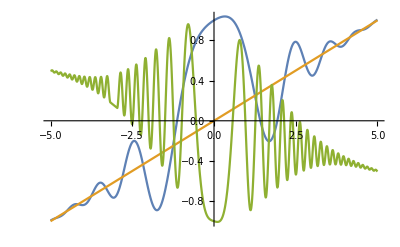

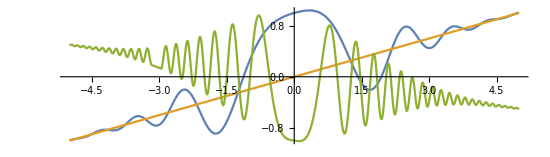

{DisplayFunction→Identity,Ticks→{Automatic,Automatic},AxesOrigin→{0,0},FrameTicks→{{Automatic,Charting`ScaledFrameTicks[{Identity,Identity}]},{Automatic,Charting`ScaledFrameTicks[{Identity,Identity}]}},GridLines→{None,None},DisplayFunction→Identity,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},PlotRangeClipping→True,ImagePadding→All,DisplayFunction→Identity,AspectRatio→2/7,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0,0},DisplayFunction:>Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],ImageSize→550,Method→{DefaultBoundaryStyle→Automatic,DefaultGraphicsInteraction→{Version→1.2,TrackMousePosition→{True,False},Effects→{Highlight→{ratio→2},HighlightPoint→{ratio→2},Droplines→{freeformCursorMode→True,placement→{x→All,y→None}}}},DefaultMeshStyle→AbsolutePointSize[6],ScalingFunctions→None,CoordinatesToolOptions→{DisplayFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),CopiedValueFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}},PlotRange→{{-5,5},{-1.00678,1.03866}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]}},Ticks→{Automatic,Automatic}}

Absolute[{DisplayFunction→Identity,Ticks→{Automatic,Automatic},AxesOrigin→{0,0},FrameTicks→{{Automatic,Charting`ScaledFrameTicks[{Identity,Identity}]},{Automatic,Charting`ScaledFrameTicks[{Identity,Identity}]}},GridLines→{None,None},DisplayFunction→Identity,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},PlotRangeClipping→True,ImagePadding→All,DisplayFunction→Identity,AspectRatio→2/7,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0,0},DisplayFunction:>Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],ImageSize→550,Method→{DefaultBoundaryStyle→Automatic,DefaultGraphicsInteraction→{Version→1.2,TrackMousePosition→{True,False},Effects→{Highlight→{ratio→2},HighlightPoint→{ratio→2},Droplines→{freeformCursorMode→True,placement→{x→All,y→None}}}},DefaultMeshStyle→AbsolutePointSize[6],ScalingFunctions→None,CoordinatesToolOptions→{DisplayFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),CopiedValueFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}},PlotRange→{{-5,5},{-1.00678,1.03866}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]}},Ticks→{Automatic,Automatic}}]

{PlotRange→{{-5,5},{-1.00678,1.03866}},AspectRatio→2/7}

```mathematica
Clear["Global`*"]
RandomInteger[{7,25},20]
Sort[%,Less]

f1[x_]:=Cos[x^2]/E^(0.2*x^2)+0.2*x
f2[x_]:=0.2*x
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
Plot[{f1[x],f2[x],f3[x]},{x,-5,5}]
grf1D:=Plot[{f1[x],f2[x],f3[x]},{x,-5,5},AspectRatio->2/7,ImageSize->550];
grf1D
(*вскрывем код*)
Options[grf1D]

Options[grf1D,{PlotRange,AspectRatio}]
```

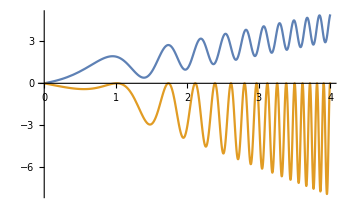
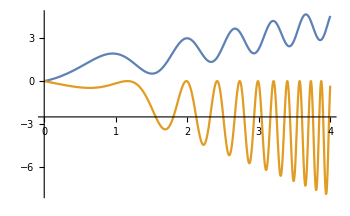

```mathematica
grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},BaseStyle->18,ImageSize->350];
grf2=Plot[{x+Sin[2*x^2],x*Sin[x^3]-x},{x,0,4},BaseStyle->18,ImageSize->350,AxesOrigin->{0,-2.5}];
Row[{grf1,grf2},Spacer[15]]
```

```mathematica
AxesOrigin->{0,-2.5}//InputForm
```

AxesOrigin -> {0, -2.5}

```mathematica
p=40353607;q=1/9;
#^q&[p]
```

7

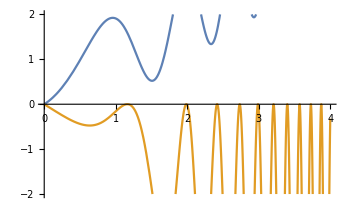
-Graphics--Graphics-

```mathematica
grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},BaseStyle->18,ImageSize->350];
grf2=Plot[{x+Sin[2*x^2],x*Sin[x^3]-x},{x,0,4},BaseStyle->18,ImageSize->350,PlotRange->{-2,2}];
Row[{grf1,grf2},Spacer[15]]
```

```mathematica
FullSimplify[3^(-1+x)/338384*(3-8/(2+3^x)^4-4/(2+3^x)^3-(2+3^x)^(-1)-(2*Log[3]^2)/(3^x*Log[3]+Log[9])^2)]/.x->2//InputForm
```

3/117128

```mathematica
Manipulate[Expand[(x+α*y)^n],{{n,18,"Степень n"},0,50,1,Appearance->"Labeled"},{{α,5,"Множитель α"},-3,5,0.1,Appearance->"Labeled"},BaseStyle->{Red,Bold,18},LabelStyle->Directive[Blue,Plain,Italic,16]]
```

```mathematica
Clear[a,b,c,d,x];
fRab:=a*x^3-(c+x^3)/(d+x^2)+(a+x^3)/(d+x^3);
Position[fRab,x^3,3]
InputForm[fRab]
```

{{1,2},{2,3,2},{3,1,2}}

a*x^3 - (c + x^3)/(d + x^2) + (a + x^3)/(d + x^3)

```mathematica
StringLength["LabelStyle→{27,Bold}"]
```

20

```mathematica
lstR={{1,4,73,9,-1,41,-7,-73,45,11,-2,40,3,-7,2,-5,11,5,41,8,42,73}};
Select[lstR,x_/;OddQ[x]&&x<41]
```

False

```mathematica
LetterNumber
```

```mathematica
CharacterName
```

Part::pspec1: Part specification Grf2 (+оформление) is not applicable.

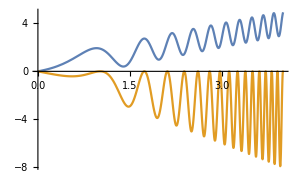
-Graphics--Graphics-

```mathematica
grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},ImageSize->300];
grf2=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},ImageSize->300,PlotLegends->Style[["Grf2 (+оформление)"]]];
Row[{grf1,grf2},Spacer[5]]
```

```mathematica
OptionsPattern
```

```mathematica
Manipulate[Sum[k^n,{k,0,m}],{n,4,30,1}]
Manipulate[Sum[k^n,{k,0,m}],{n,4,30,1},LabelStyle->{27,Bold}]
```